## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* circular construction *)
```

```mathematica
CircularArc[R_,nnφ_,{mx_,my_,mz_}]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePoly,Final, Final2},
z=0;
dφ=2.*π/nnφ;
φ = dφ;
SlicePoly={};
For[k=0,k≤(nnφ-1),k++;
SlicePoly=Append[SlicePoly,{R*Cos[φ],R*Sin[φ]}];
φ+=dφ;
];
Print["SlicePoly: ", SlicePoly];
Final = {};
Final = Append[Final, {SlicePoly, 0.}];
Final = Append[Final, {SlicePoly, 1}];

Final2={};
Final2 = Append[Final, {SlicePoly, 0.7}];
Final2 = Append[Final, {SlicePoly, 1.0}];
Print["Final: ", Final]; 
radObjMltExtPgn[Final, N[{mx,my,mz}]]
]
radUtiDelAll[];
arrSlice = CircularArc[1., 12,{1., 0., 0.}]
Print["arrSlice object index number: ", arrSlice]
radObjDrwAtr[arrSlice, {0, 0.5, 0.8}]
```

SlicePoly: {{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}}

Final: {{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},0.},{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},1}}

2

arrSlice object index number: 2

2

```mathematica
(* Plot the circular piece, to visualize *)
```

```mathematica
RadPlot3DOptions[];
dr = radObjDrw[arrSlice];
Show[Graphics3D[dr, PlotLabel ->"Slice", BaseStyle -> {14, FontFamily-> "Times"}]]
```

-Graphics3D-

```mathematica
(* single segment of the array *)
```

```mathematica
φ = 0
dφ = π/6
R = 10
mx = Cos[φ+dφ/2]
my =Sin[φ+dφ/2]
mz = 0
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment = Append[segment, {segment[[1]][[1]], R}]
final = radObjMltExtPgn[segment, {mx, my, mz}]
radObjDrwAtr[final, {0, 0.5, 0.8}]
RadPlot3DOptions[];
s = radObjDrw[final];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

4

4

-Graphics3D-

```mathematica
(* Plot the magnetic field *)
```

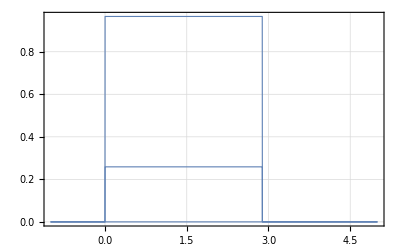

```mathematica
RadPlotOptions[];
Plot[radFld[final, "m", {5,y, 5}], {y, -1, 5}]
```

```mathematica
(* 2 segments of the Halbach array by hand *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 10
mx1 = Cos[φ+dφ/2]
my1 =Sin[φ+dφ/2]
mz1 = 0

(* create first segment, place same shape at z=0, z=R *)
segment1 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment1 = Append[segment1, {segment1[[1]][[1]], R}]

(* Iterate on the variables for the second segment *)
φ += dφ
mx2 = Cos[φ+dφ/2]
my2 =Sin[φ+dφ/2]
mz2 = 0

(* add new segments at z=0, z=R *)
segment2 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment2 = Append[segment2, {segment2[[1]][[1]], R}]
Print["segment is now: ", segment2]

(* first attempt to create segments, then define group for segments *)
s1 = radObjMltExtPgn[segment1, {mx1, my1, mz1}]
s2 = radObjMltExtPgn[segment2, {mx2, my2, mz2}]
group = radObjCnt[{s1, s2}]


(* color the object *)
radObjDrwAtr[group, {0, 0.5, 0.8}]

(* plot + show the object *)
RadPlot3DOptions[];
s = radObjDrw[group];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

π/6

1/(√2)

1/(√2)

0

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0}}

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

segment is now: {{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

6

8

9

9

-Graphics3D-

```mathematica
(* Plot the magnetic field's x-component *)
```

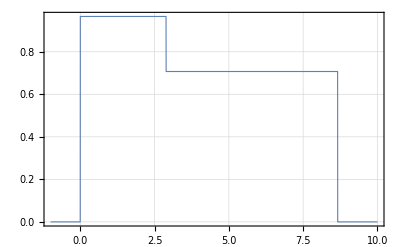

```mathematica
RadPlotOptions[];
Plot[radFld[group, "mx", {5,y, 5}], {y, -1, 10}]
```

```mathematica
(* Draw all 12 segments of the array, outward pointing magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[φ+dφ/2];
my =Sin[φ+dφ/2];
mz = 0;

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

25.4

10

-Graphics3D-

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

35

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the magnetic field to demonstrate spatial rotation *)
```

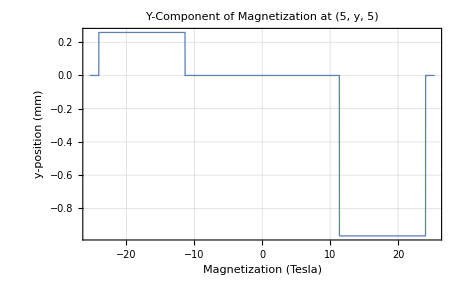

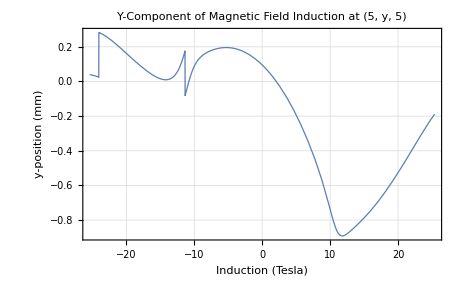

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "my", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetization at (5, y, 5)", AxesLabel->{"Magnetization (Tesla)", "y-position (mm)"}]
Plot[radFld[halbach, "By", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetic Field Induction at (5, y, 5)", AxesLabel->{"Induction (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

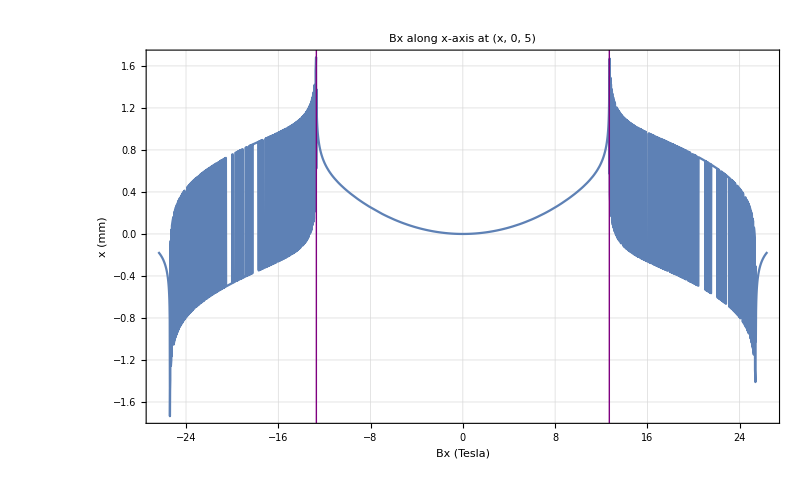

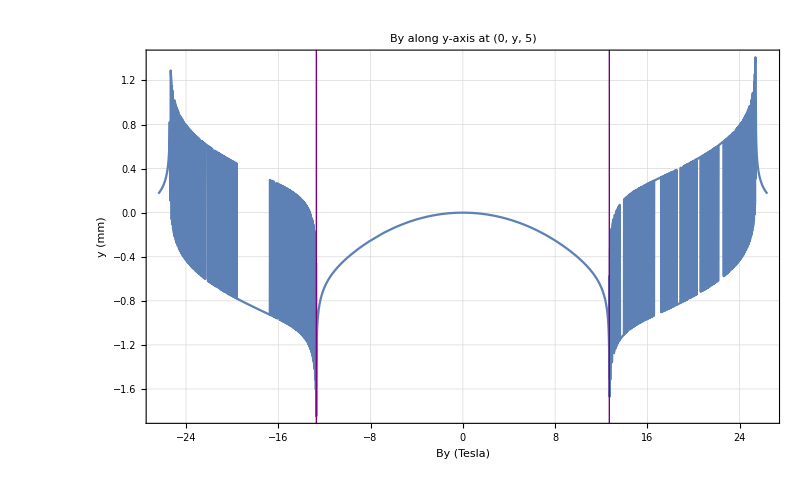

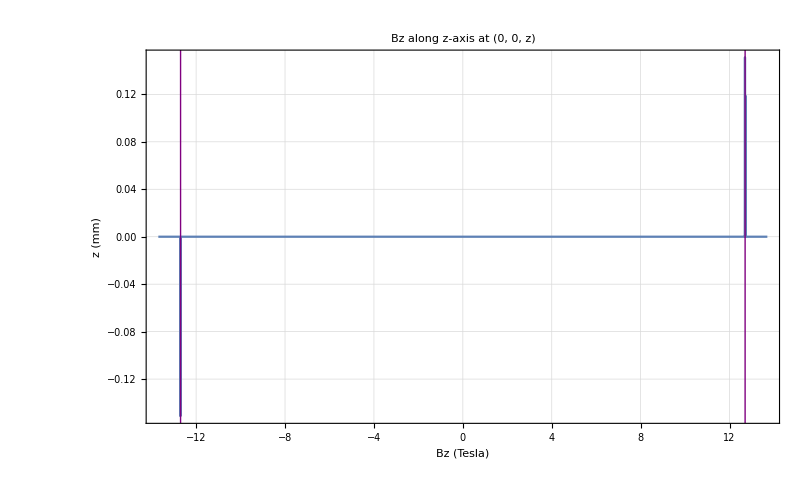

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "Bx", {x, 0, 5}], {x, -R -1, R + 1}, PlotLabel->"Bx along x-axis at (x, 0, 5)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "By", {0, y, 5}], {y, -R -1, R + 1}, PlotLabel->"By along y-axis at (0, y, 5)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "Bz", {0, 0, z}], {z, -R/2  - 1, R/2 + 1}, PlotLabel->"Bz along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

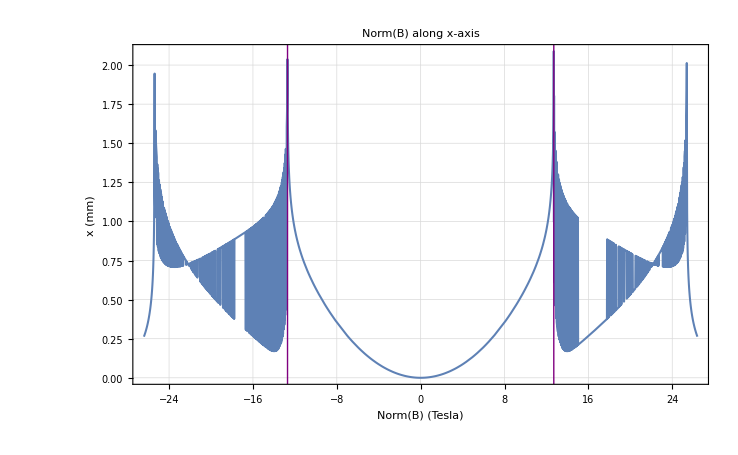

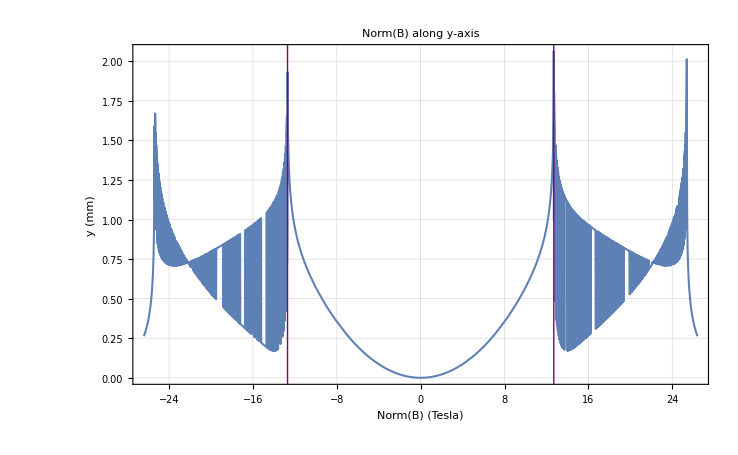

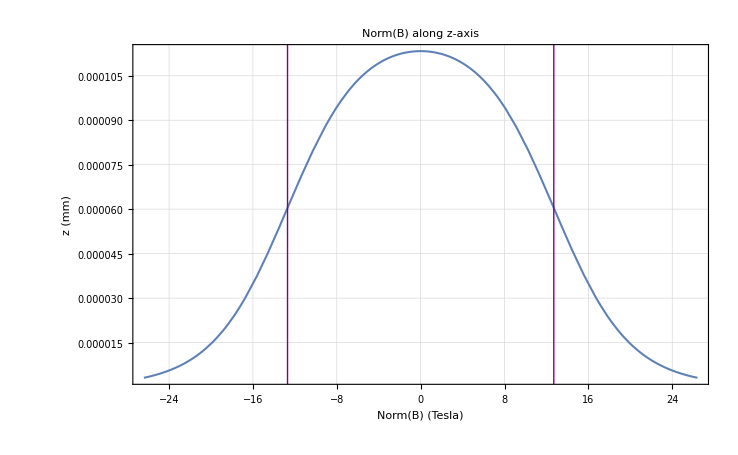

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "Bx", {x, y, z}];
by = radFld[halbach, "By", {x, y, z}];
bz = radFld[halbach, "Bz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 5], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 5], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-R/2,-10},{-R/2,10}}],Line[{{R/2,-10},{R/2,10}}]}]
```

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a .csv file *)
```

```mathematica
(* initialize variables *)
xStart = -R/2;
yStart = -R/2;
zStart = -R/2;
m=5;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};
bMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ m, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bx", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ m, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ m, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "By", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ m, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bz", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ m, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ m, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
norm[xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)]]
];
];
];

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bMatrix=Append[bMatrix, {}];
For[j=1, j≤ m, j++,
bMatrix[[i]]=Append[bMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bMatrix[[i]][[j]]=Append[bMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "B", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]
Print["bMatrix: ", MatrixForm[bMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/bmatrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
Export["bMatrix.fits",bMatrix];
```

bxMatrix: ((0.248943
-0.263648
-0.23192
-0.263648
0.248943) | (0.966988
0.928685
0.949411
0.928685
0.966988) | (1.75542
4.16223
4.42829
3.52685
2.79428) | (0.167364
0.0610622
0.0709387
0.0610622
-0.0914546) | (-0.603122
-0.510579
-0.498683
-0.510579
-0.603122)
(-0.0383836
-0.364671
-0.347173
-0.364671
-0.297203) | (0.171916
0.302975
0.328115
0.302975
0.171916) | (0.086208
0.150957
0.164162
0.150957
0.086208) | (-0.171995
-0.312
-0.331731
-0.312
-0.171995) | (0.482136
0.066074
0.0264346
0.066074
-0.48379)
(-1.47887
-3.95653
-3.14694
-3.76638
-2.26711) | (-0.0861858
-0.148813
-0.163144
-0.148813
-0.0861858) | (-0.241481
-0.120741
0.362222
-2.6262×10^-13
4.36068×10^-13) | (-0.0861858
-0.148813
-0.163144
-0.148813
-0.0861858) | (-2.49072
-3.64253
-3.92477
-3.26168
-2.08899)
(-0.48379
0.066074
0.0264346
0.066074
-0.48379) | (-0.171995
-0.312
-0.331731
-0.312
-0.171995) | (0.086208
0.150957
0.164162
0.150957
0.086208) | (0.171916
0.302975
0.328115
0.302975
0.171916) | (-0.297203
-0.364671
-0.347173
-0.364671
-0.297203)
(0.103985
-0.510579
-0.498683
-0.510579
-0.603122) | (-0.0914546
0.0610622
0.0709387
0.0610622
-0.0914546) | (2.51048
3.751
4.25752
4.19589
2.56862) | (0.966988
0.928685
0.949411
0.928685
0.966988) | (0.248943
-0.263648
-0.23192
-0.263648
-0.458163))

byMatrix: ((-0.248943
0.263648
0.23192
0.263648
-0.248943) | (0.297203
0.364671
0.347173
0.364671
0.297203) | (2.2767
3.37657
3.52221
3.76727
1.64804) | (0.48379
-0.066074
-0.0264346
-0.066074
-0.482136) | (0.603122
0.510579
0.498683
0.510579
0.603122)
(-0.00106265
-0.928685
-0.949411
-0.928685
-0.966988) | (-0.171916
-0.302975
-0.328115
-0.302975
-0.171916) | (0.0861858
0.148813
0.163144
0.148813
0.0861858) | (0.171995
0.312
0.331731
0.312
0.171995) | (0.0914546
-0.0610622
-0.0709387
-0.0610622
-0.167364)
(-1.7787
-4.29636
-3.57813
-3.32371
-1.89519) | (-0.086208
-0.150957
-0.164162
-0.150957
-0.086208) | (0.0883883
0.120741
-0.209129
0.056036
0.176777) | (-0.086208
-0.150957
-0.164162
-0.150957
-0.086208) | (-2.6831
-3.85298
-4.39427
-4.28521
-2.31606)
(-0.167364
-0.0610622
-0.0709387
-0.0610622
-0.167364) | (0.171995
0.312
0.331731
0.312
0.171995) | (0.0861858
0.148813
0.163144
0.148813
0.0861858) | (-0.171916
-0.302975
-0.328115
-0.302975
-0.171916) | (-0.966988
-0.928685
-0.949411
-0.928685
-0.966988)
(-0.103985
0.510579
0.498683
0.510579
0.603122) | (-0.482136
-0.066074
-0.0264346
-0.066074
-0.482136) | (1.73769
3.89952
3.75371
3.45608
1.97667) | (0.297203
0.364671
0.347173
0.364671
0.297203) | (-0.248943
0.263648
0.23192
0.263648
0.458163))

bzMatrix: ((-7.87949×10^-12
1.88265×10^-11
-4.01064×10^-13
-7.27165×10^-12
3.0869×10^-12) | (-0.469829
-0.0746736
-8.77398×10^-12
0.0746736
0.469829) | (-3.75763
-0.0579236
-9.48877×10^-12
0.0579236
3.77376) | (0.38392
0.0538753
9.11177×10^-12
-0.0538753
-0.38392) | (0.201604
0.0776941
1.00794×10^-11
-0.0776941
-0.201604)
(0.469829
0.0746736
1.78039×10^-11
-0.0746736
-0.469829) | (1.42814×10^-12
3.98147×10^-11
1.26664×10^-11
1.28013×10^-13
1.50415×10^-11) | (-0.0279691
-0.0111912
6.16256×10^-12
0.0111912
0.0279691) | (0.130633
0.0401618
8.731×10^-12
-0.0401618
-0.130633) | (0.38392
0.0538753
8.48952×10^-12
-0.0538753
-0.38392)
(3.94298
0.0579236
2.21613×10^-11
-0.0579236
-3.80462) | (0.0279691
0.0111912
1.83783×10^-11
-0.0111912
-0.0279691) | (-5.0585×10^-11
1.13045×10^-11
1.00484×10^-11
6.13737×10^-12
1.1088×10^-11) | (-0.0279691
-0.0111912
8.89127×10^-12
0.0111912
0.0279691) | (-3.73241
-0.0579236
1.05969×10^-11
0.0579236
3.77056)
(-0.38392
-0.0538753
1.70666×10^-11
0.0538753
0.38392) | (-0.130633
-0.0401618
1.26674×10^-11
0.0401618
0.130633) | (0.0279691
0.0111912
7.61876×10^-12
-0.0111912
-0.0279691) | (2.46203×10^-11
2.09896×10^-11
7.55986×10^-12
-4.15087×10^-12
4.16547×10^-12) | (-0.469829
-0.0746736
9.46417×10^-12
0.0746736
0.469829)
(-0.201604
-0.0776941
2.06127×10^-11
0.0776941
0.201604) | (-0.38392
-0.0538753
8.4465×10^-12
0.0538753
0.38392) | (3.60919
0.0579236
3.7286×10^-12
-0.0579236
-3.62529) | (0.469829
0.0746736
5.09674×10^-12
-0.0746736
-0.469829) | (-3.9088×10^-12
8.85204×10^-12
5.33197×10^-12
-3.57005×10^-12
-8.35707×10^-12))

normbMatrix: ((0.352059
0.372854
0.327984
0.372854
0.352059) | (1.11541
1.00051
1.0109
1.00051
1.11541) | (4.7743
5.39695
5.67976
4.73681
4.77123) | (0.639889
0.104866
0.0757039
0.104866
0.623068) | (0.876445
0.726236
0.705244
0.726236
0.876445)
(0.471396
1.00051
1.0109
1.00051
1.11541) | (0.243126
0.428472
0.464024
0.428472
0.243126) | (0.125068
0.21227
0.231442
0.21227
0.125068) | (0.276097
0.443059
0.469138
0.443059
0.276097) | (0.623068
0.104866
0.0757039
0.104866
0.639889)
(4.53677
4.96048
5.38609
4.80036
5.12332) | (0.125068
0.21227
0.231442
0.21227
0.125068) | (0.156474
0.306186
0.311272
0.259177
0.125) | (0.125068
0.21227
0.231442
0.21227
0.125068) | (4.92258
5.23682
5.0606
5.60511
4.61821)
(0.639889
0.104866
0.0757039
0.104866
0.639889) | (0.276097
0.443059
0.469138
0.443059
0.276097) | (0.125068
0.21227
0.231442
0.21227
0.125068) | (0.243126
0.428472
0.464024
0.428472
0.243126) | (1.11541
1.00051
1.0109
1.00051
1.11541)
(0.249539
0.726236
0.705244
0.726236
0.876445) | (0.623068
0.104866
0.0757039
0.104866
0.623068) | (4.69647
5.03332
5.25114
5.84897
4.39119) | (1.11541
1.00051
1.0109
1.00051
1.11541) | (0.352059
0.372854
0.327984
0.372854
0.521427))

bMatrix: ((0.248943 | -0.248943 | -2.69242×10^-11
-0.263648 | 0.263648 | 7.53498×10^-12
-0.23192 | 0.23192 | -4.01149×10^-13
-0.263648 | 0.263648 | -9.41747×10^-12
0.248943 | -0.248943 | -2.60101×10^-11) | (0.966988 | 0.297203 | -0.469829
0.928685 | 0.364671 | -0.0746736
0.949411 | 0.347173 | -7.72292×10^-12
0.928685 | 0.364671 | 0.0746736
0.966988 | 0.297203 | 0.469829) | (1.56815 | 2.27965 | -3.75571
4.40861 | 3.63947 | -0.0579236
3.96257 | 3.90762 | -1.03984×10^-11
3.92368 | 4.00784 | 0.0579236
2.53191 | 2.07281 | 3.7964) | (0.167364 | 0.48379 | 0.38392
0.0610622 | -0.066074 | 0.0538753
0.0709387 | -0.0264346 | 5.9816×10^-12
0.0610622 | -0.066074 | -0.0538753
-0.0914546 | -0.482136 | -0.38392) | (-0.603122 | 0.603122 | 0.201604
-0.510579 | 0.510579 | 0.0776941
-0.498683 | 0.498683 | 5.01617×10^-12
-0.510579 | 0.510579 | -0.0776941
-0.603122 | 0.603122 | -0.201604)
(-0.0383836 | -0.00106265 | 0.469829
-0.364671 | -0.928685 | 0.0746736
-0.347173 | -0.949411 | 2.06066×10^-11
-0.364671 | -0.928685 | -0.0746736
-0.297203 | -0.966988 | -0.469829) | (0.171916 | -0.171916 | 1.96435×10^-11
0.302975 | -0.302975 | 3.57851×10^-11
0.328115 | -0.328115 | 1.26659×10^-11
0.302975 | -0.302975 | 8.69006×10^-12
0.171916 | -0.171916 | 4.92198×10^-12) | (0.086208 | 0.0861858 | -0.0279691
0.150957 | 0.148813 | -0.0111912
0.164162 | 0.163144 | 5.10085×10^-12
0.150957 | 0.148813 | 0.0111912
0.086208 | 0.0861858 | 0.0279691) | (-0.171995 | 0.171995 | 0.130633
-0.312 | 0.312 | 0.0401618
-0.331731 | 0.331731 | 1.03895×10^-11
-0.312 | 0.312 | -0.0401618
-0.171995 | 0.171995 | -0.130633) | (0.482136 | 0.0914546 | 0.38392
0.066074 | -0.0610622 | 0.0538753
0.0264346 | -0.0709387 | 6.94402×10^-12
0.066074 | -0.0610622 | -0.0538753
-0.48379 | -0.167364 | -0.38392)
(-1.59034 | -1.794 | 3.87453
-3.0512 | -3.38416 | 0.0579236
-3.943 | -4.01377 | 2.2173×10^-11
-3.96725 | -3.90164 | -0.0579236
-2.34976 | -2.47231 | -3.858) | (-0.0861858 | -0.086208 | 0.0279691
-0.148813 | -0.150957 | 0.0111912
-0.163144 | -0.164162 | 1.83866×10^-11
-0.148813 | -0.150957 | -0.0111912
-0.0861858 | -0.086208 | -0.0279691) | (0.362222 | 0.0323524 | -4.94494×10^-11
1.36933×10^-12 | 8.22403×10^-12 | 1.13045×10^-11
0.273834 | 0.426927 | 1.00483×10^-11
-0.241481 | -0.176777 | 6.13559×10^-12
0.0883883 | 0.0236836 | 1.0806×10^-11) | (-0.0861858 | -0.086208 | -0.0279691
-0.148813 | -0.150957 | -0.0111912
-0.163144 | -0.164162 | 8.69598×10^-12
-0.148813 | -0.150957 | 0.0111912
-0.0861858 | -0.086208 | 0.0279691) | (-1.65937 | -1.7112 | -3.74369
-3.30964 | -3.35653 | -0.0579236
-3.15361 | -3.39585 | 1.15828×10^-11
-3.47782 | -4.51329 | 0.0579236
-2.11643 | -1.87685 | 3.76118)
(-0.48379 | -0.167364 | -0.38392
0.066074 | -0.0610622 | -0.0538753
0.0264346 | -0.0709387 | 1.61962×10^-11
0.066074 | -0.0610622 | 0.0538753
-0.48379 | -0.167364 | 0.38392) | (-0.171995 | 0.171995 | -0.130633
-0.312 | 0.312 | -0.0401618
-0.331731 | 0.331731 | 1.12853×10^-11
-0.312 | 0.312 | 0.0401618
-0.171995 | 0.171995 | 0.130633) | (0.086208 | 0.0861858 | 0.0279691
0.150957 | 0.148813 | 0.0111912
0.164162 | 0.163144 | 7.41722×10^-12
0.150957 | 0.148813 | -0.0111912
0.086208 | 0.0861858 | -0.0279691) | (0.171916 | -0.171916 | 1.31084×10^-12
0.302975 | -0.302975 | 1.91661×10^-11
0.328115 | -0.328115 | 7.56007×10^-12
0.302975 | -0.302975 | 8.72698×10^-13
0.171916 | -0.171916 | 2.9906×10^-11) | (-0.297203 | -0.966988 | -0.469829
-0.364671 | -0.928685 | -0.0746736
-0.347173 | -0.949411 | 9.08275×10^-12
-0.364671 | -0.928685 | 0.0746736
-0.297203 | -0.966988 | 0.469829)
(0.103985 | -0.103985 | -0.201604
-0.510579 | 0.510579 | -0.0776941
-0.498683 | 0.498683 | 1.89364×10^-11
-0.510579 | 0.510579 | 0.0776941
-0.603122 | 0.603122 | 0.201604) | (-0.0914546 | -0.482136 | -0.38392
0.0610622 | -0.066074 | -0.0538753
0.0709387 | -0.0264346 | 7.23669×10^-12
0.0610622 | -0.066074 | 0.0538753
-0.0914546 | -0.482136 | 0.38392) | (2.23908 | 2.36699 | 3.58966
4.04601 | 4.02973 | 0.0579236
4.05803 | 3.87398 | 2.10837×10^-12
4.27906 | 3.48608 | -0.0579236
2.37649 | 2.34892 | -3.6464) | (0.966988 | 0.297203 | 0.469829
0.928685 | 0.364671 | 0.0746736
0.949411 | 0.347173 | 1.06153×10^-11
0.928685 | 0.364671 | -0.0746736
0.966988 | 0.297203 | -0.469829) | (0.248943 | -0.248943 | 2.25737×10^-11
-0.263648 | 0.263648 | 1.85126×10^-11
-0.23192 | 0.23192 | 5.33163×10^-12
-0.263648 | 0.263648 | -1.31289×10^-11
0.248943 | -0.248943 | 3.33857×10^-11))